```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[ParentDirectory[NotebookDirectory[]]<>"/Data/"<>"Table_standing_variants.txt","CSV"];
```

## Rescue probability for varying seed bank size and resistance cost

### Parameters and functions for rescue from standing variation that do not vary with seed bank size and resistance cost

#### Parameters of the model

```mathematica
b=0.9 140;
dZ=0.35;
gZ = 0.2;
f=0.9 13000;
dS=0.94;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
g = 0.3;
p=0.95;
dB=0.48;
μ=0;
hl=0.998;
ht=0.985;
kh=0.5;
densPlants=1;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Standing genetic variation

```mathematica
pos=Table[Position[dataStandingVariation⟦All,{1,2}⟧,{0.95,c}]⟦1,1⟧,{c,{0.001,0.05,0.1,0.15,0.2,0.25,0.3}}];
v = {dataStandingVariation[[pos,3]],dataStandingVariation[[pos,4]],dataStandingVariation[[pos,5]]};
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[[j]]/(1-β);
Γ[i_]:=Exp[Sum[λm[i,j](γ[[j]]/(1-β)-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities

```mathematica
q={q1,q2,q3,(α[[1]]q1+γ[[1]])/(1-β),(α[[2]]q2+γ[[2]])/(1-β),(α[[3]]q3+γ[[3]])/(1-β)}/.Table[FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet,{c,{0.001,0.05,0.1,0.15,0.2,0.25,0.3}}];
```

### Rescue from standing variation for an initial seed bank of 10 seeds per square meter

#### Seed bank density

```mathematica
densSeeds=10;
```

#### Rescue probability from standing variation

```mathematica
pRescue[A_,q_,l_]:=1- Exp[A  (densPlants  (v[[1,l]]  (q[[1]]-1)+ v[[2,l]]  (q[[2]]-1)+v[[3,l]]  (q[[3]]-1))+densSeeds  (v[[1,l]]  (q[[4]]-1)+ v[[2,l]] (q[[5]]-1)+v[[3,l]]  (q[[6]]-1)))]//Quiet;
```

#### Rescue probability from standing variation for varying resistance costs

```mathematica
pRstanding1=MapThread[pRescue[10^5,#1,#2]&,{q,Range[1,Length[pos]]}];
```

### Rescue from standing variation for an initial seed bank of 100 seeds per square meter

#### Seed bank density

```mathematica
densSeeds=100;
```

#### Rescue probability from standing variation

```mathematica
pRescue[A_,q_,l_]:=1- Exp[A  (densPlants  (v[[1,l]]  (q[[1]]-1)+ v[[2,l]]  (q[[2]]-1)+v[[3,l]]  (q[[3]]-1))+densSeeds  (v[[1,l]]  (q[[4]]-1)+ v[[2,l]] (q[[5]]-1)+v[[3,l]]  (q[[6]]-1)))]//Quiet;
```

#### Rescue probability from standing variation for varying resistance costs

```mathematica
pRstanding2=MapThread[pRescue[10^5,#1,#2]&,{q,Range[1,Length[pos]]}];
```

### Parameters and functions for rescue from de novo mutations that do not vary with seed bank size and resistance cost

#### Parameters of the model

```mathematica
b=140a;
f=13000a;
```

```mathematica
c=0.3;
cr = {0,kc c,c};
```

```mathematica
S = (1-cr)f(1-dS);
```

```mathematica
μ=10^-8;
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

#### Parameters of the reduced set of equations for the extinction probabilities

```mathematica
Λ[i_,j_]:=λ[i,j]+λm[i,j]α[[j]]/(1-β);
Γ[i_]:=Exp[Sum[λm[i,j](γ[[j]]/(1-β)-1)-λ[i,j],{j,1,3}]];
```

#### Extinction probabilities

```mathematica
q={q1,q2,q3,(α[[1]]q1+γ[[1]])/(1-β),(α[[2]]q2+γ[[2]])/(1-β),(α[[3]]q3+γ[[3]])/(1-β)}/.Table[FindRoot[{q1==Γ[1]Exp[Λ[1,1] q1+Λ[1,2] q2+Λ[1,3] q3],q2==Γ[2]Exp[Λ[2,1] q1+Λ[2,2] q2+Λ[2,3] q3],q3==Γ[3]Exp[Λ[3,1] q1+Λ[3,2] q2+Λ[3,3] q3]},{{q1,0},{q2,0},{q3,0}}]//Quiet,{a,{0.5,0.7,0.9}}];
```

### Rescue from de novo mutations for an initial seed bank of 10 seeds per square meter

#### Seed bank density

```mathematica
densSeeds=10;
```

#### Rescue probability from de novo mutations

```mathematica
pRescue[A_,q_]:=1- Exp[A  (densPlants  (q[[1]]-1)+densSeeds  ((q[[4]]-1)))]//Quiet;
```

#### Rescue probability from de novo mutations for varying resistance costs

```mathematica
pRdenovo1=pRescue[10^5,#]&/@q;
```

### Rescue from de novo mutations for an initial seed bank of 100 seeds per square meter

#### Seed bank density

```mathematica
densSeeds=100;
```

#### Rescue probability from de novo mutations for varying resistance costs

```mathematica
pRdenovo2=pRescue[10^5,#]&/@q;
```

### Bar chart for the rescue probability with an initial seed bank of 10 seeds per square meter

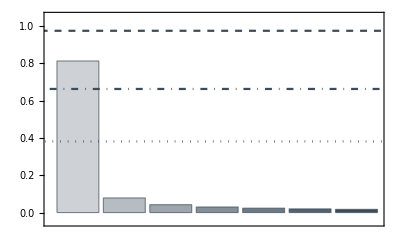

```mathematica
barChart1=BarChart[pRstanding1,BarSpacing->Automatic,ChartBaseStyle->EdgeForm[RGBColor["#3C4C59"]],ChartStyle->Reverse[Table[ Lighter[RGBColor["#3C4C59"],i],{i,0.,0.75,0.125}]],GridLines->{{},{{pRdenovo1[[3]],Dashed},{pRdenovo1[[2]],DotDashed},{pRdenovo1[[1]],Dotted}}},GridLinesStyle->Directive[RGBColor["#3C4C59"],Thickness[0.004]],Method->{"GridLinesInFront"->True},PlotRange->{Automatic,{-.05,1.05}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None]
```

### Bar chart for the rescue probability with an initial seed bank of 100 seeds per square meter

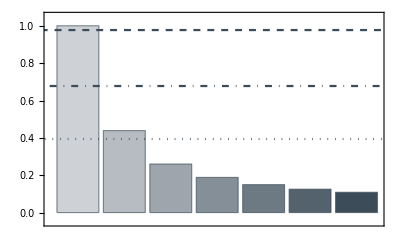

```mathematica
barChart2=BarChart[pRstanding2,BarSpacing->Automatic,ChartBaseStyle->EdgeForm[RGBColor["#3C4C59"]],ChartStyle->Reverse[Table[ Lighter[RGBColor["#3C4C59"],i],{i,0.,0.75,0.125}]],GridLines->{{},{{pRdenovo2[[3]],Dashed},{pRdenovo2[[2]],DotDashed},{pRdenovo2[[1]],Dotted}}},GridLinesStyle->Directive[RGBColor["#3C4C59"],Thickness[0.004]],Method->{"GridLinesInFront"->True},PlotRange->{Automatic,{-.05,1.05}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None]
```